```mathematica
"definição do estádio"
a=1
b=1
```

definição do estádio

1

1

```mathematica
"definição da base utilizada"
φ[x_,y_,n_,m_]=(x+√(y(b-y)))^n(x-a-√(y(b-y)))y^m(y-b)
nM=3
mM=3
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
```

definição da base utilizada

(-1+y) y^m (-1+x-√((1-y) y)) (x+√((1-y) y))^n

3

3

{(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^3,(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^3,(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^3}

```mathematica
"definição da matriz A"
A[k_] = Table[∫_0^b ∫_(-√(y(b-y)))^(a+√(y(b-y))) φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]Laplacian[φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{x,y}]ⅆxⅆy+k^2∫_0^b ∫_(-√(y(b-y)))^(a+√(y(b-y))) φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM]ⅆxⅆy ,{i,0,nM*mM-1},{j,0,nM*mM-1}]
A[k] // MatrixForm
```

definição da matriz A

{{-101/504+k^2 (281/18900+(1163 π)/245760)-(391 π)/6144,-3739/18900+k^2 (6001/415800+(1129 π)/245760)-(1933 π)/30720,-2449/10800+k^2 (1667/103950+(2509 π)/491520)-(8867 π)/122880,-101/1008+k^2 (281/37800+(1163 π)/491520)-(391 π)/12288,-3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440,-2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760,-571/10800+k^2 (214/51975+(5153 π)/3932160)-(1373 π)/81920,-1037/19800+k^2 (21503/5405400+(4979 π)/3932160)-(8183 π)/491520,-14269/237600+k^2 (41633/9459450+(38561 π)/27525120)-(7513 π)/393216},{-3739/18900+k^2 (6001/415800+(1129 π)/245760)-(1933 π)/30720,-1153/4725+k^2 (1667/103950+(2509 π)/491520)-(4771 π)/61440,1/840 (-1859419/6930-(10931 π)/128)+k^2 (19693/1009008+(1425 π)/229376),-3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440,-1153/9450+k^2 (1667/207900+(2509 π)/983040)-(4771 π)/122880,1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752),-839/16632+k^2 (21503/5405400+(4979 π)/3932160)-(2627 π)/163840,-73/1155+k^2 (41633/9459450+(38561 π)/27525120)-(6589 π)/327680,-12605189/151351200+k^2 (8075/1513512+(9349 π)/5505024)-(18239 π)/688128},{-2449/10800+k^2 (1667/103950+(2509 π)/491520)-(8867 π)/122880,1/840 (-1859419/6930-(10931 π)/128)+k^2 (19693/1009008+(1425 π)/229376),-446161/970200+k^2 (12799/504504+(44455 π)/5505024)-(25181 π)/172032,-2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760,1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752),-446161/1940400+k^2 (12799/1009008+(44455 π)/11010048)-(25181 π)/344064,-31337/554400+k^2 (41633/9459450+(38561 π)/27525120)-(2357 π)/131072,-948041/11642400+k^2 (8075/1513512+(9349 π)/5505024)-(22291 π)/860160,-996517/8408400+k^2 (83/12012+(774911 π)/352321536)-(346097 π)/9175040},{-101/1008+k^2 (281/37800+(1163 π)/491520)-(391 π)/12288,-3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440,-2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760,-569/8400+k^2 (214/51975+(5153 π)/3932160)-(2641 π)/122880,-3911/59400+k^2 (21503/5405400+(4979 π)/3932160)-(343 π)/16384,-123619/1663200+k^2 (41633/9459450+(38561 π)/27525120)-(1453 π)/61440,-119/2700+k^2 (409/166320+(1231 π)/1572864)-(6863 π)/491520,-17701/415800+k^2 (10201/4324320+(1181 π)/1572864)-(4433 π)/327680,-39637/831600+k^2 (98101/37837800+(45431 π)/55050240)-(59621 π)/3932160},{-3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440,-1153/9450+k^2 (1667/207900+(2509 π)/983040)-(4771 π)/122880,1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752),-3911/59400+k^2 (21503/5405400+(4979 π)/3932160)-(343 π)/16384,-8237/103950+k^2 (41633/9459450+(38561 π)/27525120)-(4957 π)/196608,1/840 (-15418811/180180-(223109 π)/8192)+k^2 (8075/1513512+(9349 π)/5505024),-173/4158+k^2 (10201/4324320+(1181 π)/1572864)-(12997 π)/983040,-10361/207900+k^2 (98101/37837800+(45431 π)/55050240)-(31169 π)/1966080,1/840 (-4817591/90090-(8713 π)/512)+k^2 (1801/576576+(3649 π)/3670016)},{-2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760,1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752),-446161/1940400+k^2 (12799/1009008+(44455 π)/11010048)-(25181 π)/344064,-123619/1663200+k^2 (41633/9459450+(38561 π)/27525120)-(1453 π)/61440,1/840 (-15418811/180180-(223109 π)/8192)+k^2 (8075/1513512+(9349 π)/5505024),(-3629501/5005-(1890849 π)/8192)/5040+k^2 (83/12012+(774911 π)/352321536),-4241/92400+k^2 (98101/37837800+(45431 π)/55050240)-(19137 π)/1310720,1/840 (-4747427/90090-(137377 π)/8192)+k^2 (1801/576576+(3649 π)/3670016),-74141/840840+k^2 (8117/2018016+(902173 π)/704643072)-(514981 π)/18350080},{-571/10800+k^2 (214/51975+(5153 π)/3932160)-(1373 π)/81920,-839/16632+k^2 (21503/5405400+(4979 π)/3932160)-(2627 π)/163840,-31337/554400+k^2 (41633/9459450+(38561 π)/27525120)-(2357 π)/131072,-119/2700+k^2 (409/166320+(1231 π)/1572864)-(6863 π)/491520,-173/4158+k^2 (10201/4324320+(1181 π)/1572864)-(12997 π)/983040,-4241/92400+k^2 (98101/37837800+(45431 π)/55050240)-(19137 π)/1310720,-13753/415800+k^2 (17/10920+(1039 π)/2097152)-(41147 π)/3932160,-55931/1801800+k^2 (2287/1544400+(14827 π)/31457280)-(38767 π)/3932160,-855979/25225200+k^2 (10183/6306300+(301809 π)/587202560)-(396071 π)/36700160},{-1037/19800+k^2 (21503/5405400+(4979 π)/3932160)-(8183 π)/491520,-73/1155+k^2 (41633/9459450+(38561 π)/27525120)-(6589 π)/327680,-948041/11642400+k^2 (8075/1513512+(9349 π)/5505024)-(22291 π)/860160,-17701/415800+k^2 (10201/4324320+(1181 π)/1572864)-(4433 π)/327680,-10361/207900+k^2 (98101/37837800+(45431 π)/55050240)-(31169 π)/1966080,1/840 (-4747427/90090-(137377 π)/8192)+k^2 (1801/576576+(3649 π)/3670016),-55931/1801800+k^2 (2287/1544400+(14827 π)/31457280)-(38767 π)/3932160,-340159/9459450+k^2 (10183/6306300+(301809 π)/587202560)-(629579 π)/55050240,-125553/2802800+k^2 (198743/102918816+(216563 π)/352321536)-(18683 π)/1310720},{-14269/237600+k^2 (41633/9459450+(38561 π)/27525120)-(7513 π)/393216,-12605189/151351200+k^2 (8075/1513512+(9349 π)/5505024)-(18239 π)/688128,-996517/8408400+k^2 (83/12012+(774911 π)/352321536)-(346097 π)/9175040,-39637/831600+k^2 (98101/37837800+(45431 π)/55050240)-(59621 π)/3932160,1/840 (-4817591/90090-(8713 π)/512)+k^2 (1801/576576+(3649 π)/3670016),-74141/840840+k^2 (8117/2018016+(902173 π)/704643072)-(514981 π)/18350080,1/560 (-855979/45045-(396071 π)/65536)+k^2 (10183/6306300+(301809 π)/587202560),-125553/2802800+k^2 (198743/102918816+(216563 π)/352321536)-(18683 π)/1310720,-774101/12612600+k^2 (381223/154378224+(6646499 π)/8455716864)-(819301 π)/41943040}}

(-101/504+k^2 (281/18900+(1163 π)/245760)-(391 π)/6144 | -3739/18900+k^2 (6001/415800+(1129 π)/245760)-(1933 π)/30720 | -2449/10800+k^2 (1667/103950+(2509 π)/491520)-(8867 π)/122880 | -101/1008+k^2 (281/37800+(1163 π)/491520)-(391 π)/12288 | -3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440 | -2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760 | -571/10800+k^2 (214/51975+(5153 π)/3932160)-(1373 π)/81920 | -1037/19800+k^2 (21503/5405400+(4979 π)/3932160)-(8183 π)/491520 | -14269/237600+k^2 (41633/9459450+(38561 π)/27525120)-(7513 π)/393216
-3739/18900+k^2 (6001/415800+(1129 π)/245760)-(1933 π)/30720 | -1153/4725+k^2 (1667/103950+(2509 π)/491520)-(4771 π)/61440 | 1/840 (-1859419/6930-(10931 π)/128)+k^2 (19693/1009008+(1425 π)/229376) | -3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440 | -1153/9450+k^2 (1667/207900+(2509 π)/983040)-(4771 π)/122880 | 1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752) | -839/16632+k^2 (21503/5405400+(4979 π)/3932160)-(2627 π)/163840 | -73/1155+k^2 (41633/9459450+(38561 π)/27525120)-(6589 π)/327680 | -12605189/151351200+k^2 (8075/1513512+(9349 π)/5505024)-(18239 π)/688128
-2449/10800+k^2 (1667/103950+(2509 π)/491520)-(8867 π)/122880 | 1/840 (-1859419/6930-(10931 π)/128)+k^2 (19693/1009008+(1425 π)/229376) | -446161/970200+k^2 (12799/504504+(44455 π)/5505024)-(25181 π)/172032 | -2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760 | 1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752) | -446161/1940400+k^2 (12799/1009008+(44455 π)/11010048)-(25181 π)/344064 | -31337/554400+k^2 (41633/9459450+(38561 π)/27525120)-(2357 π)/131072 | -948041/11642400+k^2 (8075/1513512+(9349 π)/5505024)-(22291 π)/860160 | -996517/8408400+k^2 (83/12012+(774911 π)/352321536)-(346097 π)/9175040
-101/1008+k^2 (281/37800+(1163 π)/491520)-(391 π)/12288 | -3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440 | -2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760 | -569/8400+k^2 (214/51975+(5153 π)/3932160)-(2641 π)/122880 | -3911/59400+k^2 (21503/5405400+(4979 π)/3932160)-(343 π)/16384 | -123619/1663200+k^2 (41633/9459450+(38561 π)/27525120)-(1453 π)/61440 | -119/2700+k^2 (409/166320+(1231 π)/1572864)-(6863 π)/491520 | -17701/415800+k^2 (10201/4324320+(1181 π)/1572864)-(4433 π)/327680 | -39637/831600+k^2 (98101/37837800+(45431 π)/55050240)-(59621 π)/3932160
-3739/37800+k^2 (6001/831600+(1129 π)/491520)-(1933 π)/61440 | -1153/9450+k^2 (1667/207900+(2509 π)/983040)-(4771 π)/122880 | 1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752) | -3911/59400+k^2 (21503/5405400+(4979 π)/3932160)-(343 π)/16384 | -8237/103950+k^2 (41633/9459450+(38561 π)/27525120)-(4957 π)/196608 | 1/840 (-15418811/180180-(223109 π)/8192)+k^2 (8075/1513512+(9349 π)/5505024) | -173/4158+k^2 (10201/4324320+(1181 π)/1572864)-(12997 π)/983040 | -10361/207900+k^2 (98101/37837800+(45431 π)/55050240)-(31169 π)/1966080 | 1/840 (-4817591/90090-(8713 π)/512)+k^2 (1801/576576+(3649 π)/3670016)
-2449/21600+k^2 (1667/207900+(2509 π)/983040)-(8867 π)/245760 | 1/840 (-1859419/13860-(10931 π)/256)+k^2 (19693/2018016+(1425 π)/458752) | -446161/1940400+k^2 (12799/1009008+(44455 π)/11010048)-(25181 π)/344064 | -123619/1663200+k^2 (41633/9459450+(38561 π)/27525120)-(1453 π)/61440 | 1/840 (-15418811/180180-(223109 π)/8192)+k^2 (8075/1513512+(9349 π)/5505024) | (-3629501/5005-(1890849 π)/8192)/5040+k^2 (83/12012+(774911 π)/352321536) | -4241/92400+k^2 (98101/37837800+(45431 π)/55050240)-(19137 π)/1310720 | 1/840 (-4747427/90090-(137377 π)/8192)+k^2 (1801/576576+(3649 π)/3670016) | -74141/840840+k^2 (8117/2018016+(902173 π)/704643072)-(514981 π)/18350080
-571/10800+k^2 (214/51975+(5153 π)/3932160)-(1373 π)/81920 | -839/16632+k^2 (21503/5405400+(4979 π)/3932160)-(2627 π)/163840 | -31337/554400+k^2 (41633/9459450+(38561 π)/27525120)-(2357 π)/131072 | -119/2700+k^2 (409/166320+(1231 π)/1572864)-(6863 π)/491520 | -173/4158+k^2 (10201/4324320+(1181 π)/1572864)-(12997 π)/983040 | -4241/92400+k^2 (98101/37837800+(45431 π)/55050240)-(19137 π)/1310720 | -13753/415800+k^2 (17/10920+(1039 π)/2097152)-(41147 π)/3932160 | -55931/1801800+k^2 (2287/1544400+(14827 π)/31457280)-(38767 π)/3932160 | -855979/25225200+k^2 (10183/6306300+(301809 π)/587202560)-(396071 π)/36700160
-1037/19800+k^2 (21503/5405400+(4979 π)/3932160)-(8183 π)/491520 | -73/1155+k^2 (41633/9459450+(38561 π)/27525120)-(6589 π)/327680 | -948041/11642400+k^2 (8075/1513512+(9349 π)/5505024)-(22291 π)/860160 | -17701/415800+k^2 (10201/4324320+(1181 π)/1572864)-(4433 π)/327680 | -10361/207900+k^2 (98101/37837800+(45431 π)/55050240)-(31169 π)/1966080 | 1/840 (-4747427/90090-(137377 π)/8192)+k^2 (1801/576576+(3649 π)/3670016) | -55931/1801800+k^2 (2287/1544400+(14827 π)/31457280)-(38767 π)/3932160 | -340159/9459450+k^2 (10183/6306300+(301809 π)/587202560)-(629579 π)/55050240 | -125553/2802800+k^2 (198743/102918816+(216563 π)/352321536)-(18683 π)/1310720
-14269/237600+k^2 (41633/9459450+(38561 π)/27525120)-(7513 π)/393216 | -12605189/151351200+k^2 (8075/1513512+(9349 π)/5505024)-(18239 π)/688128 | -996517/8408400+k^2 (83/12012+(774911 π)/352321536)-(346097 π)/9175040 | -39637/831600+k^2 (98101/37837800+(45431 π)/55050240)-(59621 π)/3932160 | 1/840 (-4817591/90090-(8713 π)/512)+k^2 (1801/576576+(3649 π)/3670016) | -74141/840840+k^2 (8117/2018016+(902173 π)/704643072)-(514981 π)/18350080 | 1/560 (-855979/45045-(396071 π)/65536)+k^2 (10183/6306300+(301809 π)/587202560) | -125553/2802800+k^2 (198743/102918816+(216563 π)/352321536)-(18683 π)/1310720 | -774101/12612600+k^2 (381223/154378224+(6646499 π)/8455716864)-(819301 π)/41943040)

```mathematica
"autovalores obtidos numericamente"
NSolve[Det[A[k]]== 0 && k ≥ 0,k]
```

autovalores obtidos numericamente

{{k→3.59471},{k→4.78594},{k→6.37409},{k→6.60694},{k→7.72399},{k→9.28114},{k→9.71426},{k→10.765},{k→12.3079}}

```mathematica
"autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia"
ka=12.30794348875186
Vc[ka]=NullSpace[A[ka]]
id=1
v=Vc[ka][[id]]
ϕ[x_,y_]=Base[x,y].v
```

autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia

12.3079

{{0.0516885,-0.13034,0.0716159,-0.230858,0.578294,-0.316048,0.230858,-0.578294,0.316048}}

1

{0.0516885,-0.13034,0.0716159,-0.230858,0.578294,-0.316048,0.230858,-0.578294,0.316048}

0.0516885 (-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))-0.230858 (-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))+0.230858 (-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))-0.13034 (-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^2+0.578294 (-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^2-0.578294 (-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^2+0.0716159 (-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^3-0.316048 (-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^3+0.316048 (-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^3

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

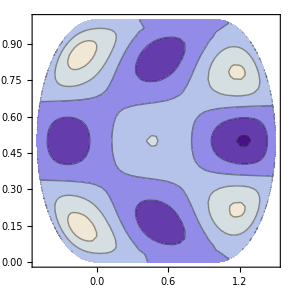

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

linhas nodais da autofunção

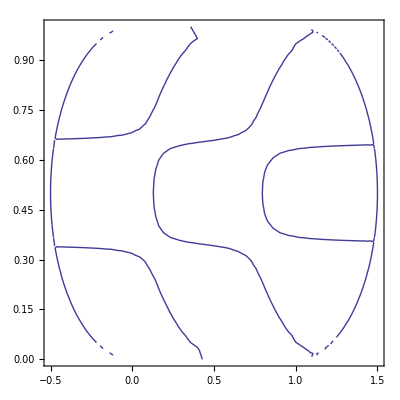

```mathematica
"linhas nodais da autofunção"
ContourPlot[ϕ[x,y]== 0,{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

```mathematica
"curvas de nível das autofunções"
```